```mathematica
Integrate[Exp[-Sqrt[R^2+r^2-2 r R Cos[θ]]/L] r/(R^2+r^2-2 r R Cos[θ])Sin[θ],{θ,0,π},Assumptions->{r>0,R>0,L>0,R>r}]
```

(-ExpIntegralEi[(r-R)/L]+ExpIntegralEi[-(r+R)/L])/R

```mathematica
Integrate[2 π Exp[-Sqrt[R^2+r^2-2 r R Cos[θ]]/L]/L r^2/(4 π (R^2+r^2-2 r R Cos[θ]))Sin[θ],{θ,0,π},Assumptions->{r>0,R>0,L>0,R>r}]
```

(r (-ExpIntegralEi[(r-R)/L]+ExpIntegralEi[-(r+R)/L]))/(2 L R)

```mathematica
NIntegrate[%26 /. R->6.05 /. L->.263, {r,0,6.05}]
```

0.489132

```mathematica
Integrate[Exp[-Sqrt[R^2+r^2-2 r R Cos[θ]]/L]/L(r^2 Sin[θ] Abs[(R Cos[θ] - r)])/((R^2+r^2-2 r R Cos[θ])^(3/2)),{θ,0,π},Assumptions->{r>0,R>0,L>0,R>r}]
```

```mathematica
Integrate[
```

1/(2 L^2 R √(-r^2+R^2))ⅇ^(-r/L-R/L-(√(-r^2+R^2))/L) (2 ⅇ^(r/L+R/L) L r^2-2 ⅇ^(r/L+R/L) L R^2+2 ⅇ^(r/L+R/L) L^2 √(-r^2+R^2)-ⅇ^((√(-r^2+R^2))/L) L^2 √(-r^2+R^2)-ⅇ^((2 r)/L+(√(-r^2+R^2))/L) L^2 √(-r^2+R^2)-ⅇ^((√(-r^2+R^2))/L) L r √(-r^2+R^2)+ⅇ^((2 r)/L+(√(-r^2+R^2))/L) L r √(-r^2+R^2)+ⅇ^((√(-r^2+R^2))/L) L R √(-r^2+R^2)+ⅇ^((2 r)/L+(√(-r^2+R^2))/L) L R √(-r^2+R^2)-ⅇ^(r/L+R/L+(√(-r^2+R^2))/L) r^2 √(-r^2+R^2) ExpIntegralEi[(r-R)/L]+ⅇ^(r/L+R/L+(√(-r^2+R^2))/L) R^2 √(-r^2+R^2) ExpIntegralEi[(r-R)/L]-ⅇ^(r/L+R/L+(√(-r^2+R^2))/L) r^2 √(-r^2+R^2) ExpIntegralEi[-(r+R)/L]+ⅇ^(r/L+R/L+(√(-r^2+R^2))/L) R^2 √(-r^2+R^2) ExpIntegralEi[-(r+R)/L]+2 ⅇ^(r/L+R/L+(√(-r^2+R^2))/L) r^2 √(-r^2+R^2) ExpIntegralEi[-(√(-r^2+R^2))/L]-2 ⅇ^(r/L+R/L+(√(-r^2+R^2))/L) R^2 √(-r^2+R^2) ExpIntegralEi[-(√(-r^2+R^2))/L])

```mathematica
Integrate[Exp[-Sqrt[R^2+r^2-2 r R Cos[θ]]/L]/L(r Sin[θ])/((R^2+r^2-2 r R Cos[θ])^(1/2)),{θ,0,π},Assumptions->{r>0,R>0,L>0,R>r}]
```

(ⅇ^(-(r+R)/L) (-1+ⅇ^((2 r)/L)))/R

```mathematica
Integrate[Exp[-Sqrt[R^2+r^2-2 r R Cos[θ]]/L](Sin[θ] Abs[(R Cos[θ] - r)])/((R^2+r^2-2 r R Cos[θ])^(1/2)),{θ,0,π},Assumptions->{r>0,R>0,L>0,R>r}]
```

1/(r^2 R)ⅇ^(-r/L-R/L-(√(-r^2+R^2))/L) L (2 ⅇ^(r/L+R/L) L^2-ⅇ^((√(-r^2+R^2))/L) L^2-ⅇ^((2 r)/L+(√(-r^2+R^2))/L) L^2-ⅇ^((√(-r^2+R^2))/L) L r+ⅇ^((2 r)/L+(√(-r^2+R^2))/L) L r-ⅇ^((√(-r^2+R^2))/L) r^2-ⅇ^((2 r)/L+(√(-r^2+R^2))/L) r^2-ⅇ^((√(-r^2+R^2))/L) L R-ⅇ^((2 r)/L+(√(-r^2+R^2))/L) L R-ⅇ^((√(-r^2+R^2))/L) r R+ⅇ^((2 r)/L+(√(-r^2+R^2))/L) r R+2 ⅇ^(r/L+R/L) L √(-r^2+R^2))

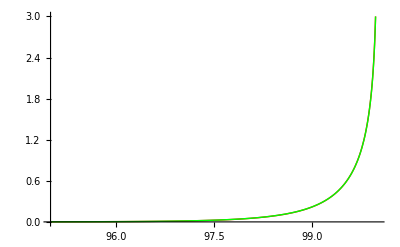

```mathematica
Plot[Evaluate[{%24/NIntegrate[%24 /. R->100 /. L -> 1,{r,90,100}],%12/NIntegrate[%12 /. R->100 /. L -> 1,{r,90,100}]}/. R->100 /. L ->1], {r,95,100},PlotStyle->{{Red,Thick},{Thick,Green}},PlotRange->{0,3}]
```

```mathematica
D[ArcSin[(r Sin[θ])/(R^2+r^2-2 r R Cos[θ])],θ]
```

((r Cos[θ])/(r^2+R^2-2 r R Cos[θ])-(2 r^2 R Sin[θ]^2)/((r^2+R^2-2 r R Cos[θ])^2))/(√(1-(r^2 Sin[θ]^2)/((r^2+R^2-2 r R Cos[θ])^2)))

```mathematica
FullSimplify[%]
```

(r (-2 r R+(r^2+R^2) Cos[θ]))/((r^2+R^2-2 r R Cos[θ])^2 √(1-(r^2 Sin[θ]^2)/((r^2+R^2-2 r R Cos[θ])^2)))

```mathematica
D[ArcSin[(r Sin[θ])/(R^2+r^2-2 r R Cos[θ])],r]
```

(-(r (2 r-2 R Cos[θ]) Sin[θ])/((r^2+R^2-2 r R Cos[θ])^2)+Sin[θ]/(r^2+R^2-2 r R Cos[θ]))/(√(1-(r^2 Sin[θ]^2)/((r^2+R^2-2 r R Cos[θ])^2)))

```mathematica
FullSimplify[%]
```

((-r^2+R^2) Sin[θ])/((r^2+R^2-2 r R Cos[θ])^2 √(1-(r^2 Sin[θ]^2)/((r^2+R^2-2 r R Cos[θ])^2)))